```mathematica
Clear["Global`*"]
θ=30 Pi/180.;
jet[t_]:=Disk[{0.9Sin[θ]t,10-0.9Cos[θ]t},0.2]
ray[t0_,t_]:={LightOrange,If[t≤t0,Opacity[0],Opacity[1]],Disk[{0.9Sin[θ]t0,Max[10-0.9Cos[θ]t0-Cos[θ](t-t0),0]},0.1]}
picture[t_]:=
Graphics[{
Table[ray[n,t],{n,0,10}],
Line[{{-10,0},{10,0}}],
jet[t],
Dashed,
Line[{{0,0},{0,10}}],
If[t>10,{
Line[{{0.9Sin[θ]10,0},{0.9Sin[θ]10,10}}],
Dashing[1],Arrowheads[{-.05,.05}],
Arrow[{{0,8},{0.9Sin[θ]10,8}}],
Text[Style["L",Large],{0.9Sin[θ]5,8.5}],
Text[Style["V_1=L/t_1",Large],{0.9Sin[θ]10,11}]
}],
Text[
Style["t_2 = "<>ToString[
If[t<11.547,
0,
If[t<12.547,
t-11.547,
1]]
],Large],{0,-1}],
Text[
Style["t_1 = "<>ToString[
If[t>10,
10,
t]],
Large],{0,11}],
If[t>12.547,
Text[Style["V_2=L/t_2",Large],{0.9Sin[θ]10,-1}]
]
},PlotRange->{{-2,7},{-2,12}}]
Manipulate[picture[t],{t,0,15}]
```

```mathematica
pictures=Table[picture[t],{t,0,15,0.1}];
Export["~/Desktop/jet_angle.gif",pictures,ImageResolution->200,"DisplayDurations"->2/20]
```

~/Desktop/jet_angle.gif

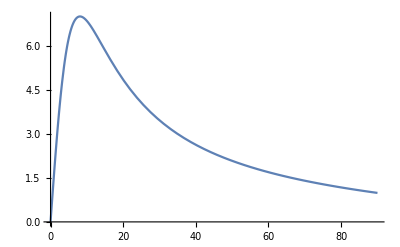

```mathematica
Plot[(0.99Sin[x Pi/180])/(1-0.99Cos[x Pi/180]),{x,0,90}]
```